```mathematica
energies = Transpose[Import["/Users/angelagraf/Desktop/main/AtomIon1D/ad_energies.dat","Table"]];
PMatrix = Import["/Users/angelagraf/Desktop/main/AtomIon1D/P_Matrix.dat","Table"];
QMatrix = Import["/Users/angelagraf/Desktop/main/AtomIon1D/Q_Matrix.dat","Table"];
RSteps = 1000
NumStates = Length[PMatrix[[2]]]
R = Flatten[Table[PMatrix[[i+((i-1)*NumStates)]],{i,1,RSteps}]];
P = Table[Table[PMatrix[[iR+(iR-1)*NumStates + i]],{i, 1, NumStates}],{iR, 1, RSteps}];
Q = Table[Table[QMatrix[[iR+(iR-1)*NumStates + i]],{i, 1, NumStates}],{iR, 1, RSteps}];
```

1000

80

```mathematica
ma=6.015122 A;
mi=170.936323 A;
ωs=2π 300000;
C4=1.121 10^-56;
C6=2.804 10^-75;
ℏ=1.054571817 10^-34;
mu2=(ma mi)/(ma+mi);
mu=Sqrt[ma/mi];
UcurvesAll[i_,j_,energies_] := Module[{f},
f = Table[Transpose[{energies[[1]], energies[[i+1 ]] -(1/(4*(2*mu*R^2)))}],{i, 1, NumStates}]
]
```

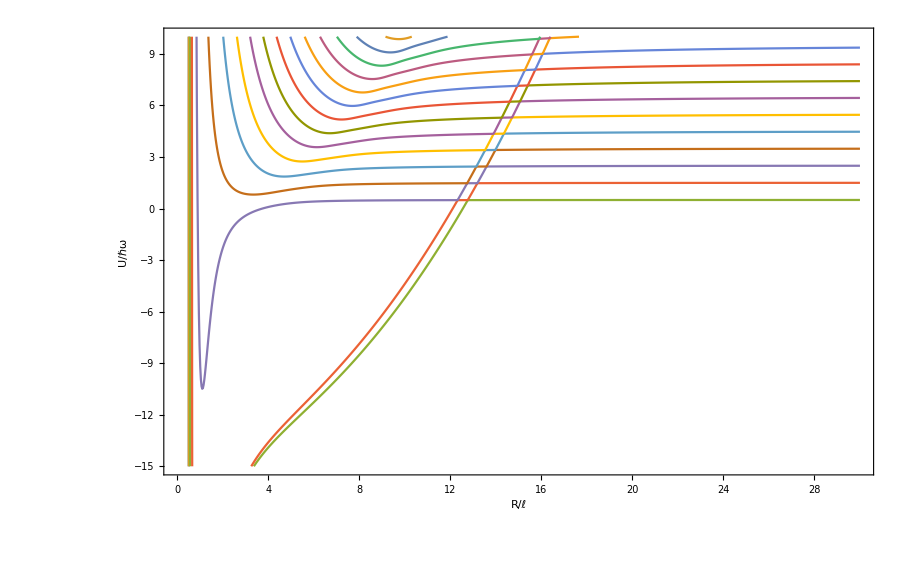

```mathematica
ListPlot [UcurvesAll[i,j,energies], Joined -> True, Frame -> True, FrameLabel -> {"R/ℓ","U/ℏω"}, LabelStyle-> Large, PlotRange -> {{0,30},{-15,10}}]
```

5.81065 A

0.187588

5.72098×10^-22 √(1/A)

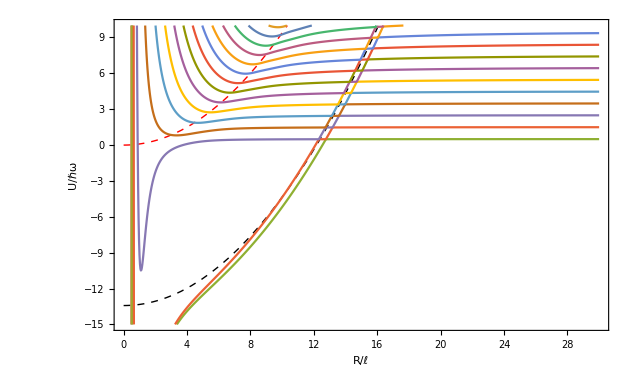

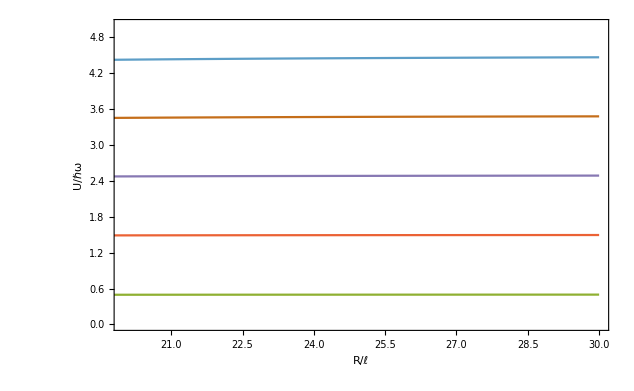

```mathematica
ma=6.015122 A;
mi=170.936323 A;
ωs=2π 300000;
C4= 1.121 10^-56;
C6=2.804 10^-75;
ℏ=1.054571817 10^-34;
mu2=(ma mi)/(ma+mi)
mu=Sqrt[ma/mi]
thetaC = ArcTan[mu];
aho=Sqrt[ℏ/(ωs mi)]

x1 = 0;
x2 = 30;
y1 = 80;
y2 = -20;

E1 = -179.5642788480468;
E0= -13.42087120307046;

(*-179.5642788480468,-13.42087120307046*)

Rstar=Sqrt[2 (mu2 C4)/ℏ^2];
sho[R_] := 1/2 R^2 mu
f0[R_] := ((1/2)*(mu)*R^2)*Cos[thetaC]^2 + E0;
f1[R_] := ((1/2)*(mu)*R^2)*Cos[thetaC]^2 + E1;
Show[Plot[sho[R], {R,0,30}, PlotRange -> {{0,30},{-15,10}},PlotStyle->{Red,Thick, Dashed}],
Plot[f0[R], {R,0,30}, PlotRange -> {{0,30},{-15,10}},PlotStyle->{Black,Thick, Dashed}],
ListPlot [UcurvesAll[i,j,energies],  PlotRange -> {{0,30},{-15,10}}, Joined -> True], Frame -> True, FrameLabel -> {"R/ℓ","U/ℏω"}, LabelStyle-> Medium ]
ListPlot [UcurvesAll[i,j,energies],  PlotRange -> {{20,x2},{0,5}}, Joined -> True, Frame -> True, FrameLabel -> {"R/ℓ","U/ℏω"},LabelStyle-> Large ]
```